布局与显示

前面我们已经看到了如何使用 Framed 来在显示对象时添加一个边框。

生成一个数字并在其周围加上边框：

```mathematica
Framed[2^100]
```

1267650600228229401496703205376

你可以给 Framed 提供选项：

指定背景颜色和边框样式：

```mathematica
Framed[2^100,Background->LightYellow,FrameStyle->LightGray]
```

1267650600228229401496703205376

Labeled 让你为对象添加一个标签。

为待边框的数字添加一个标签：

```mathematica
Labeled[Framed[2^100],"a big number"]
```

1267650600228229401496703205376a big number

这将为一个有黄色背景的数字添加一个标签：

```mathematica
Labeled[Style[2^100,Background->Yellow],"a big number"]
```

1267650600228229401496703205376a big number

这将为标签增添加样式：

```mathematica
Labeled[Style[2^100,Background->Yellow],Style["a big number",Italic,Orange]]
```

1267650600228229401496703205376a big number

你也可以在图形中使用 Labeled：

创建一个饼图，为其中一些扇形加了标签：

```mathematica
PieChart[{Labeled[1,"one"],Labeled[2,"two"],Labeled[3,Red],Labeled[4,Orange],2,2}]
```

-Graphics-

绘制带标签的点：

```mathematica
ListPlot[{Labeled[1,"one"],Labeled[2,"two"],Labeled[3,Pink],Labeled[4,Yellow],5,6,7}]
```

-Graphics-

绘制前几个素数，并标明其数值：

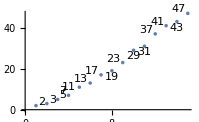

```mathematica
ListPlot[Table[Labeled[Prime[n],Prime[n]],{n,15}]]
```

Labeled 是指在某个对象旁加上标签。使用“引线式标注”往往是很好的选择，它有一条细线指向它们所指代的东西。你可以通过使用 Callout 而不是 Labeled 来创建。

Callout 将创建“引线式标注”：

```mathematica
ListPlot[Table[Callout[Prime[n],Prime[n]],{n,15}]]
```

-Graphics-

有各种各样的方法来标注图形。Style 是直接插入样式。Tooltip 用于生成交互式的工具提示，当鼠标悬停在它们上面时，它们会自动出现。Legended 是把标签放到侧面的图例中。

指定前三个扇形的样式：

```mathematica
PieChart[{Style[3,Red],Style[2,Green],Style[1,Yellow],1,2}]
```

-Graphics-

设置文字和颜色作为扇形的图例：

```mathematica
PieChart[{Legended[1,"one"],Legended[2,"two"],Legended[3,Pink],Legended[4,Yellow],2,2}]
```

-Graphics-

网络的默认绘制主题是更加明亮的颜色：

```mathematica
PieChart[{1,2,3,4,2,2},PlotTheme->"Web"]
```

-Graphics-

如果你希望 Wolfram 语言来自动选择如何标注对象，那么只需使用规则(→)来给出注释。

在 ListPlot 中，由规则指定的标注是通过引线式标注来实现的：

```mathematica
ListPlot[{1->"one",2->"two",3->Pink,4->Yellow,5,6,7}]
```

-Graphics-

在 PieChart 中，字符串被假设为标签，而颜色则是样式：

```mathematica
PieChart[{1->"one",2->"two",3->Blue,4->Red}]
```

-Graphics-

想要将不同的对象组合起来进行展示是很常见的。Row、Column 和 Grid 是实现这一目的的方便途径。

在一行中显示一系列对象：

```mathematica
Row[{Yellow,Pink,Cyan}]
```

RGBColor[1, 1, 0]RGBColor[1, 0.5, 0.5]RGBColor[0, 1, 1]

在一列中显示对象：

```mathematica
Column[{Yellow,Pink,Cyan}]
```

RGBColor[1, 1, 0]
RGBColor[1, 0.5, 0.5]
RGBColor[0, 1, 1]

使用 GraphicsRow、GraphicsColumn 和 GraphicsGrid 来排布对象，以适应一定的整体尺寸。

生成一个随机的饼图数组，自动将大小调整到合适：

```mathematica
GraphicsGrid[Table[PieChart[RandomReal[10,5]],3,6]]
```

-Graphics-

在所有对象周围添加边框：

```mathematica
GraphicsGrid[Table[PieChart[RandomReal[10,5]],3,6],Frame->All]
```

-Graphics-

词汇

Framed[expr] |   | 添加边框
Labeled[expr,lab] |   | 添加标签
Callout[expr,lab] |   | 创建标注
Tooltip[expr,lab] |   | 添加一个互动式提示条
Legended[expr,lab] |   | 添加图例
Row[{expr_1,expr_2, ...}] |   | 排成一行
Column[{expr_1,expr_2, ...}] |   | 排成一列
GraphicsRow[{expr_1,expr_2, ...}] |   | 排列在大小可调的一行中
GraphicsColumn[{expr_1,expr_2, ...}] |   | 排列在大小可调的一列中
GraphicsGrid[array] |   | 排列在大小可调的网格中

"共有 8 道习题" | "开始练习 »"

创建 100 以内的数字的列表，并为素数添加边框。 »

| 期望输出： |  
  | {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100} |

创建 100 以内的数字的列表，并为素数添加边框。 »

| 期望输出： |  
  | {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100} |

创建 100 以内的数字的列表，为素数添加边框，并添加浅灰色标签，值为它们的数值对 4 的模余。 »

| 期望输出： |  
  | {1,22,33,4,51,6,73,8,9,10,113,12,131,14,15,16,171,18,193,20,21,22,233,24,25,26,27,28,291,30,313,32,33,34,35,36,371,38,39,40,411,42,433,44,45,46,473,48,49,50,51,52,531,54,55,56,57,58,593,60,611,62,63,64,65,66,673,68,69,70,713,72,731,74,75,76,77,78,793,80,81,82,833,84,85,86,87,88,891,90,91,92,93,94,95,96,971,98,99,100} |

创建一个由 3×6 的随机彩色圆盘组成的 GraphicsGrid。 »

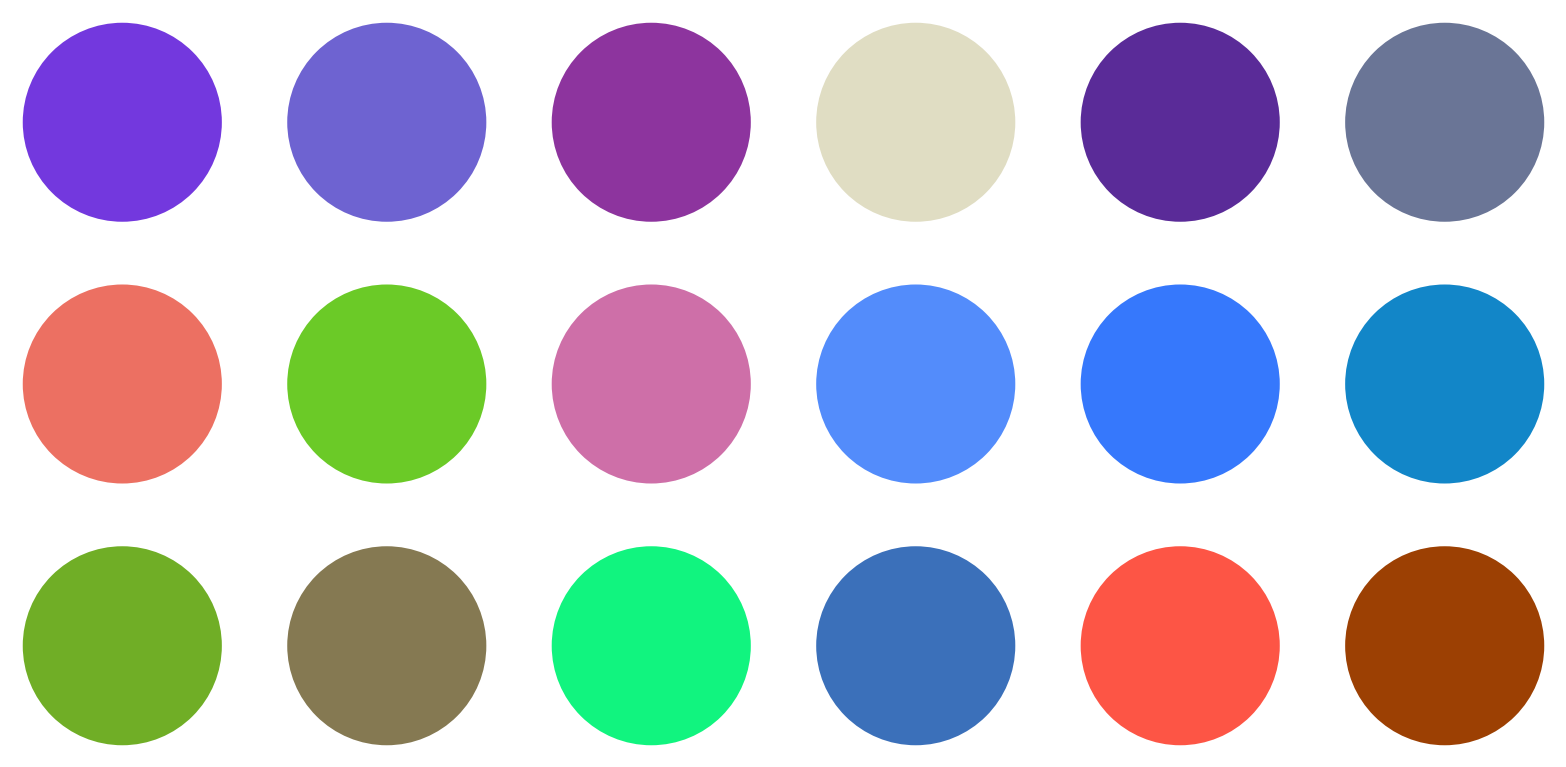
| 期望输出示例： |  
  | -Graphics- |

将 G5 中的国家的 GDP 绘制为饼图，并为每个扇形添加标签。»

| 期望输出示例： |  
  | -Graphics- |

将 G5 中的国家人口绘制为饼图，并为每个扇形添加图例。»

| 期望输出示例： |  
  | -Graphics- |

创建一个由 5×5 的饼图组成的 GraphicsGrid，给出 2^n 中各位数字的相对频率，其中 n 从 1 开始。»

| 期望输出： |  
  | -Graphics- |

将维基百科上关于 G5 的国家的文章创建为一行词云图。»

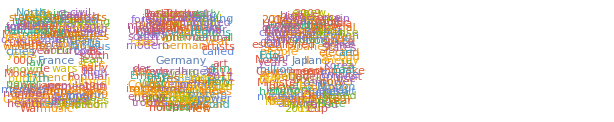
| 期望输出示例： |  
  | -Graphics- |

问&答

使用 Framed 时可以设置圆角吗？

可以的。使用 RoundingRadius→0.2 这样的选项。

哪些东西可以出现在标签中？

任何你想要的东西。标签可以是文本或图形，甚至是整个笔记本。

使用  Labeled 时可以把标签放在底部以外的地方吗？

可以。使用 Labeled[expr,label,Left] 或者 Labeled[expr,label,Right]。

我如何确定图例的位置？

使用 Placed。

可视化可以是动画的或动态的吗？

是的。ListAnimate 用于创建一个动画。从 Tooltip 到 Manipulate 的构造可以用来创建动态可视化。

技术笔记

Wolfram 语言会试图将标签放在不会干扰正在绘制的数据的位置。

你可以使用 Show[graphic,ImageSize→width] 或者 Show[graphic,ImageSize→{width,height}] 来调整任何图形的大小。ImageSize→Tiny 等也可以。

PlotTheme→"BlackBackground" 可能对弱视的人有帮助。PlotTheme→"Monochrome" 可以避免使用颜色。

ListPlot, PieChart 等会自动适用于关联(<|...|>)，在适当的时候将键值作为坐标，但在其他情况下将它们作为注释。

有很多不同种类的图例。LineLegend、BarLegend 等等。

探索更多

Wolfram 语言中的标签 & 注解向导 »